```mathematica
rule1 = {X[a_** b_]** X[c_ ]:> X[X[a **X[c]]**X[b **X[c]]]};
rule2 = {X[a_] :> {a}};
Dosh[t_]:= Simplify[(t)/.rule1]
Simp[t_]:= Simplify[(t)//.rule2]
Flog = X[x ** y] ** X[z]
Dosh[Flog]
Dosh[Dosh[Flog]]
Dosh[Dosh[Dosh[Flog]]]
Dosh[Dosh[Dosh[Dosh[Flog]]]]
```

X[x**y]**X[z]

X[X[x**X[z]]**X[y**X[z]]]

X[X[X[x**X[y**X[z]]]**X[X[z]**X[y**X[z]]]]]

X[X[X[X[x**X[X[z]**X[y**X[z]]]]**X[X[y**X[z]]**X[X[z]**X[y**X[z]]]]]]]

X[X[X[X[X[x**X[X[y**X[z]]**X[X[z]**X[y**X[z]]]]]**X[X[X[z]**X[y**X[z]]]**X[X[y**X[z]]**X[X[z]**X[y**X[z]]]]]]]]]

```mathematica
Simp[Flog]
Simp[Dosh[Flog]]
Simp[Dosh[Dosh[Flog]]]
Simp[Dosh[Dosh[Dosh[Flog]]]]
Simp[Dosh[Dosh[Dosh[Dosh[Flog]]]]]
Simp[Dosh[Dosh[Dosh[Dosh[Dosh[Flog]]]]]]
```

{x**y}**{z}

{{x**{z}}**{y**{z}}}

{{{x**{y**{z}}}**{{z}**{y**{z}}}}}

{{{{x**{{z}**{y**{z}}}}**{{y**{z}}**{{z}**{y**{z}}}}}}}

{{{{{x**{{y**{z}}**{{z}**{y**{z}}}}}**{{{z}**{y**{z}}}**{{y**{z}}**{{z}**{y**{z}}}}}}}}}

{{{{{{x**{{{z}**{y**{z}}}**{{y**{z}}**{{z}**{y**{z}}}}}}**{{{y**{z}}**{{z}**{y**{z}}}}**{{{z}**{y**{z}}}**{{y**{z}}**{{z}**{y**{z}}}}}}}}}}}

```mathematica
Boot = X[X[a**b]**c]**X[d]
Simp[Dosh[Boot]]
Simp[Dosh[Dosh[Boot]]]
Simp[Dosh[Dosh[Dosh[Boot]]]]
```

X[X[a**b]**c]**X[d]

{{{a**b}**{d}}**{c**{d}}}

{{{{a**b}**{c**{d}}}**{{d}**{c**{d}}}}}

{{{{{a**b}**{{d}**{c**{d}}}}**{{c**{d}}**{{d}**{c**{d}}}}}}}

```mathematica
Flog = X[a ** b] ** X[c** d]
Simp[Dosh[Flog]]
Simp[Dosh[Dosh[Flog]]]
Simp[Dosh[Dosh[Dosh[Flog]]]]
Simp[Dosh[Dosh[Dosh[Dosh[Flog]]]]]
Simp[Dosh[Dosh[Dosh[Dosh[Dosh[Flog]]]]]]
```

X[a**b]**X[c**d]

{{a**{c**d}}**{b**{c**d}}}

{{{a**{b**{c**d}}}**{{c**d}**{b**{c**d}}}}}

{{{{a**{{c**d}**{b**{c**d}}}}**{{b**{c**d}}**{{c**d}**{b**{c**d}}}}}}}

{{{{{a**{{b**{c**d}}**{{c**d}**{b**{c**d}}}}}**{{{c**d}**{b**{c**d}}}**{{b**{c**d}}**{{c**d}**{b**{c**d}}}}}}}}}

{{{{{{a**{{{c**d}**{b**{c**d}}}**{{b**{c**d}}**{{c**d}**{b**{c**d}}}}}}**{{{b**{c**d}}**{{c**d}**{b**{c**d}}}}**{{{c**d}**{b**{c**d}}}**{{b**{c**d}}**{{c**d}**{b**{c**d}}}}}}}}}}}

```mathematica
Freebie = X[X[a**b]**a]**X[c]
Simp[Freebie]
Dosh[Freebie]
Simp[Dosh[Freebie]]
Dosh[Dosh[Freebie]]
Simp[Dosh[Dosh[Freebie]]]
Dosh[Dosh[Dosh[Freebie]]]
Simp[Dosh[Dosh[Dosh[Freebie]]]]
```

X[X[a**b]**a]**X[c]

{{a**b}**a}**{c}

X[X[X[a**b]**X[c]]**X[a**X[c]]]

{{{a**b}**{c}}**{a**{c}}}

X[X[X[X[a**b]**X[a**X[c]]]**X[X[c]**X[a**X[c]]]]]

{{{{a**b}**{a**{c}}}**{{c}**{a**{c}}}}}

X[X[X[X[X[a**b]**X[X[c]**X[a**X[c]]]]**X[X[a**X[c]]**X[X[c]**X[a**X[c]]]]]]]

{{{{{a**b}**{{c}**{a**{c}}}}**{{a**{c}}**{{c}**{a**{c}}}}}}}

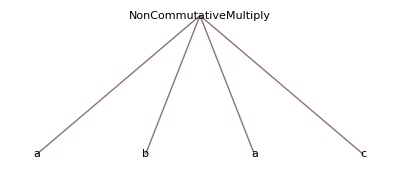

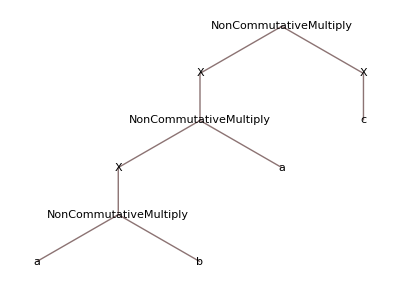

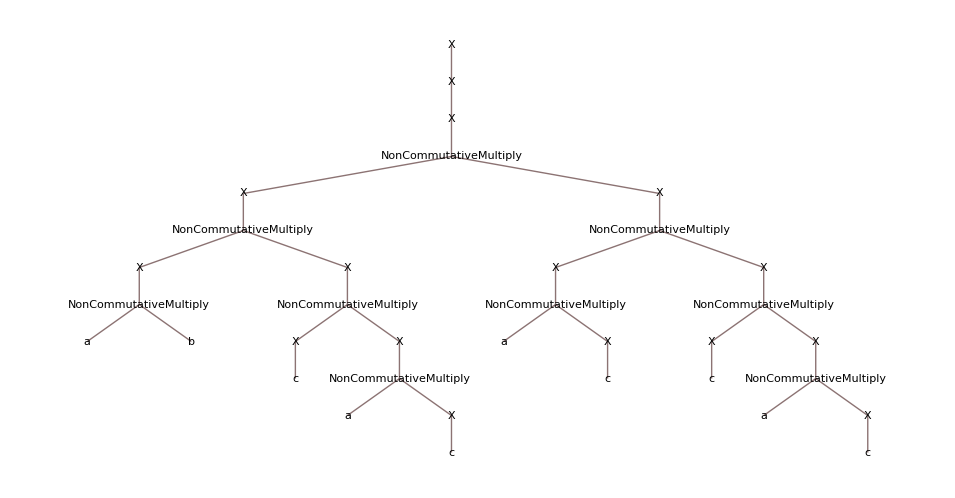

```mathematica
TreeForm[((a**b)**a)**c]
TreeForm[X[X[a**b]**a]**X[c]]
TreeForm[X[X[X[X[X[a**b]**X[X[c]**X[a**X[c]]]]**X[X[a**X[c]]**X[X[c]**X[a**X[c]]]]]]]]
```